```mathematica
ClearAll[r,ν,l,n]
hbar=197.327;
ω=1;
mass=858.6661665717603;
mass=938.858/2;

h2m2 = hbar^2/(2mass);
ν=mass*ω/(2*hbar);
l=0;
```

```mathematica
No[n_,l_,ν_]:=√(√((2 ν^3)/π)(2^(n+2l+3)n!ν^l)/((2n+2l+1)!!))
(*No[n_,l_,ν_]=1;*)
Psi[r_,n_,l_,ν_]:=r No[n,l,ν] r^l ⅇ^(-ν r^2)LaguerreL[n,l+1/2,2ν r^2] 
ddpsi[r_,n_,l_,ν_]:=Simplify[D[D[Psi[r,n,l,ν],r],r]]
V[r_]:=1/2 mass ω^2 r^2
```

```mathematica
basis={};
nm=12;
For[n=0,n<nm,n++,
AppendTo[basis,IntegerPartitions[n,{2},Table[m,{m,0,n}]] ]
]
basis=Flatten[basis,1]
```

{{0,0},{1,0},{2,0},{1,1},{3,0},{2,1},{4,0},{3,1},{2,2},{5,0},{4,1},{3,2},{6,0},{5,1},{4,2},{3,3},{7,0},{6,1},{5,2},{4,3},{8,0},{7,1},{6,2},{5,3},{4,4},{9,0},{8,1},{7,2},{6,3},{5,4},{10,0},{9,1},{8,2},{7,3},{6,4},{5,5},{11,0},{10,1},{9,2},{8,3},{7,4},{6,5}}

```mathematica
mat={};
For[col=1,col≤Length[basis],col++,{
For[row=1,row≤col,row++,{
AppendTo[mat,{row,col,Integrate[(Psi[r,basis[[row]][[1]],0,1] Psi[r,basis[[row]][[2]],0,1] Psi[r,basis[[col]][[1]],0,1] Psi[r,basis[[col]][[2]],0,1]),{r,0,Infinity}]}];
}]
}]
```

```mathematica
ListPlot3D[mat]
```

-Graphics3D-

Integral tests:

```mathematica
osziINT={};
For[ord=0,ord<12,ord++,{
part=IntegerPartitions[ord,{4},Table[n,{n,0,ord}]];
AppendTo[osziINT,Table[Integrate[(Psi[r,part[[n]][[1]],1,1] Psi[r,part[[n]][[2]],1,1] Psi[r,part[[n]][[3]],0,1] Psi[r,part[[n]][[4]],0,1]),{r,0,Infinity}],{n,Length[part]}]];
Print[ord,part];
}]
```

0{{0,0,0,0}}

1{{1,0,0,0}}

2{{2,0,0,0},{1,1,0,0}}

3{{3,0,0,0},{2,1,0,0},{1,1,1,0}}

4{{4,0,0,0},{3,1,0,0},{2,2,0,0},{2,1,1,0},{1,1,1,1}}

5{{5,0,0,0},{4,1,0,0},{3,2,0,0},{3,1,1,0},{2,2,1,0},{2,1,1,1}}

6{{6,0,0,0},{5,1,0,0},{4,2,0,0},{4,1,1,0},{3,3,0,0},{3,2,1,0},{3,1,1,1},{2,2,2,0},{2,2,1,1}}

7{{7,0,0,0},{6,1,0,0},{5,2,0,0},{5,1,1,0},{4,3,0,0},{4,2,1,0},{4,1,1,1},{3,3,1,0},{3,2,2,0},{3,2,1,1},{2,2,2,1}}

8{{8,0,0,0},{7,1,0,0},{6,2,0,0},{6,1,1,0},{5,3,0,0},{5,2,1,0},{5,1,1,1},{4,4,0,0},{4,3,1,0},{4,2,2,0},{4,2,1,1},{3,3,2,0},{3,3,1,1},{3,2,2,1},{2,2,2,2}}

9{{9,0,0,0},{8,1,0,0},{7,2,0,0},{7,1,1,0},{6,3,0,0},{6,2,1,0},{6,1,1,1},{5,4,0,0},{5,3,1,0},{5,2,2,0},{5,2,1,1},{4,4,1,0},{4,3,2,0},{4,3,1,1},{4,2,2,1},{3,3,3,0},{3,3,2,1},{3,2,2,2}}

10{{10,0,0,0},{9,1,0,0},{8,2,0,0},{8,1,1,0},{7,3,0,0},{7,2,1,0},{7,1,1,1},{6,4,0,0},{6,3,1,0},{6,2,2,0},{6,2,1,1},{5,5,0,0},{5,4,1,0},{5,3,2,0},{5,3,1,1},{5,2,2,1},{4,4,2,0},{4,4,1,1},{4,3,3,0},{4,3,2,1},{4,2,2,2},{3,3,3,1},{3,3,2,2}}

11{{11,0,0,0},{10,1,0,0},{9,2,0,0},{9,1,1,0},{8,3,0,0},{8,2,1,0},{8,1,1,1},{7,4,0,0},{7,3,1,0},{7,2,2,0},{7,2,1,1},{6,5,0,0},{6,4,1,0},{6,3,2,0},{6,3,1,1},{6,2,2,1},{5,5,1,0},{5,4,2,0},{5,4,1,1},{5,3,3,0},{5,3,2,1},{5,2,2,2},{4,4,3,0},{4,4,2,1},{4,3,3,1},{4,3,2,2},{3,3,3,2}}

{{1,{{1}}},{2,{{1}}},{3,{{2}}},{4,{{2}}},{5,{{5}}},{6,{{3}}},{7,{{9}}},{8,{{5}}},{9,{{15}}},{10,{{8}}},{11,{{23}}},{12,{{12}}}}

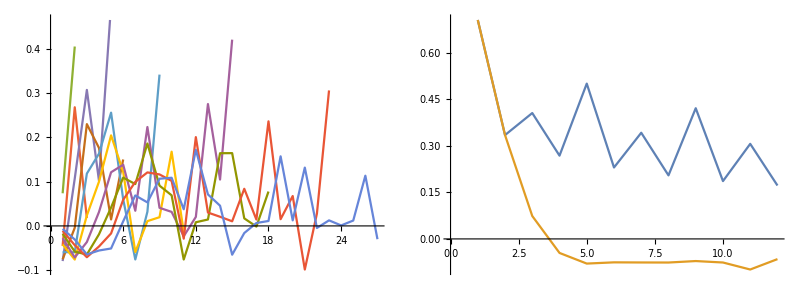

```mathematica
maxi=Table[{n,Max[osziINT[[n]]]},{n,Length[osziINT]}];
maxpos=Table[{n,Position[osziINT[[n]],maxi[[n]][[2]]]},{n,Length[osziINT]}]
mini=Table[{n,Min[osziINT[[n]]]},{n,Length[osziINT]}];
Grid[{{ListLinePlot[osziINT],ListLinePlot[{maxi,mini}]}}]
```

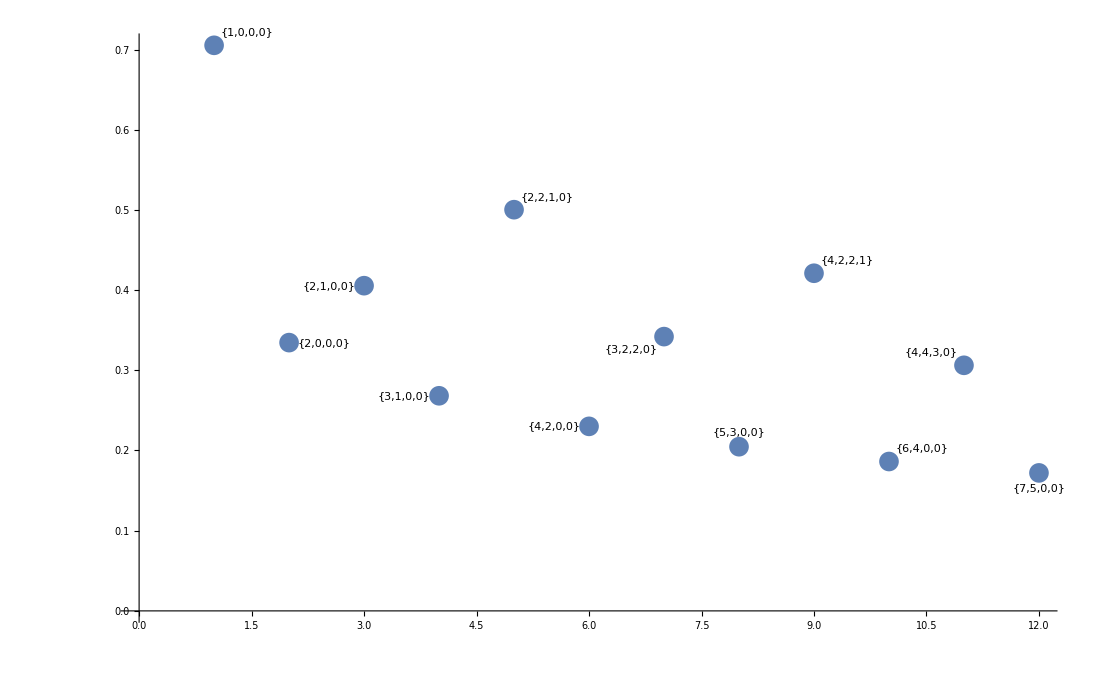

```mathematica
data=Table[Labeled[maxi[[i]],{IntegerPartitions[i,{4},Table[n,{n,0,i}]][[maxpos[[i]][[2]][[1]][[1]]]]}],{i,Length[maxi]}];
ListPlot[data,LabelingSize->90]
```

```mathematica
Vhyiama[rr_,rl_]:=((-0.3706)*Exp[-0.1808*(rr+rl)^2-0.4013*(rr-rl)^2]+(-12.94)*Exp[-0.1808*(rr+rl)^2-0.9633*(rr-rl)^2]+(-331.2)*Exp[-0.1808*(rr+rl)^2-2.930*(rr-rl)^2])
Vhyiama[rr_,rl_]:=0
```

```mathematica
Vlocal[r_]:=((-17.49)*Exp[(-0.2752*r^2)]+(-127.0)*Exp[(-0.4559*r^2)]+(497.8)*Exp[(-0.6123*r^2)])
Vlocal[r_]:=-505.1703491 Exp[-4. r^2]
```

```mathematica
Vnl[n1_,n2_]:=4 π NIntegrate[t t1 Psi[t,n1,l,ν]Vhyiama[t,t1]Psi[t1,n2,l,ν],{t,0.0,rmax},{t1,0.0,rmax}]

Vl[n1_,n2_]:= NIntegrate[Psi[t,n1,l,ν]Vlocal[t]Psi[t,n2,l,ν],{t,0.0,rmax}]
Kin[n1_,n2_]:=NIntegrate[ Psi[t,n1,l,ν]ddpsi[t,n2,l,ν],{t,0.0,rmax}]
```

```mathematica
rmax=5;
Nstate=5;
Vnl[2,2]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
l=0;
NonLocal=Table[Vnl[i,j],{i,0,Nstate},{j,0,Nstate}];
%//MatrixForm
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Local=Table[Vl[i,j],{i,0,Nstate},{j,0,Nstate}];
%//MatrixForm
```

(-115.051 | -88.3583 | -61.9461 | -41.9565 | -27.9053 | -18.3525
-88.3583 | -83.86 | -70.0107 | -55.0169 | -41.6454 | -30.7125
-61.9461 | -70.0107 | -67.0383 | -59.074 | -49.3838 | -39.7758
-41.9565 | -55.0169 | -59.074 | -57.2703 | -52.0184 | -45.1167
-27.9053 | -41.6454 | -49.3838 | -52.0184 | -50.7969 | -47.0091
-18.3525 | -30.7125 | -39.7758 | -45.1167 | -47.0091 | -46.1134)

```mathematica
Kinetic=-h2m2 Table[Kin[i,j],{i,0,Nstate},{j,0,Nstate}];
%//MatrixForm
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.09367}. NIntegrate obtained 5.66214×10^-15 and 1.9794×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.888594}. NIntegrate obtained -2.64233×10^-14 and 4.19256×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.00404341}. NIntegrate obtained 2.37588×10^-14 and 1.67439×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

(147.995 | 120.838 | -2.3483×10^-13 | 1.09587×10^-12 | -9.85365×10^-13 | -1.55759×10^-11
120.838 | 345.322 | 220.618 | -2.54169×10^-12 | -5.54843×10^-13 | 3.48331×10^-11
-7.19455×10^-15 | 220.618 | 542.649 | 319.706 | 3.01135×10^-12 | -3.30477×10^-11
-4.43184×10^-14 | -1.01299×10^-13 | 319.706 | 739.976 | 418.594 | 3.7559×10^-11
6.30242×10^-14 | 1.70367×10^-13 | -1.25473×10^-13 | 418.594 | 937.303 | 517.396
4.86495×10^-13 | 4.14406×10^-13 | -3.6554×10^-12 | 3.09158×10^-11 | 517.396 | 1134.63)

```mathematica
Hamiltonian=Local+Kinetic;
%//MatrixForm
```

(-263.046 | -209.196 | -61.9461 | -41.9565 | -27.9053 | -18.3525
-209.196 | -429.182 | -290.629 | -55.0169 | -41.6454 | -30.7125
-61.9461 | -290.629 | -609.688 | -378.78 | -49.3838 | -39.7758
-41.9565 | -55.0169 | -378.78 | -797.247 | -470.612 | -45.1167
-27.9053 | -41.6454 | -49.3838 | -470.612 | -988.1 | -564.405
-18.3525 | -30.7125 | -39.7758 | -45.1167 | -564.405 | -1180.74)

```mathematica
Sort[ Eigenvalues[Hamiltonian]]
```

{-1831.34,-1120.71,-703.619,-392.242,-175.817,-44.2727}

```mathematica
Integrate[Sin[θ] SphericalHarmonicY[0,0,θ,ϕ]Sin[θ1] SphericalHarmonicY[0,0,θ1,ϕ1],{θ1,0,π},{ϕ1,0,2 π},{θ,0,π},{ϕ,0,2 π}]
```

4 π